```mathematica
(*This is a sheet with a rod extruding from the middle of it. 
I run two versions: rod has same diffusion coefficient as sheet, rod has different diffusion coefficient from sheet*)
epsilon = 0.1;sheet = MeshRegion[{{0,0},{0,1},{1,0},{1,1}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];rod = MeshRegion[{{1,0.5-epsilon},{1,0.5+epsilon},{2,0.5-epsilon},{2,0.5+epsilon}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];
reg = RegionUnion[sheet,rod];
```

```mathematica
(*Initial Temperature Distribution*)
kk = 50;
initFunc[x_,y_]:=kk*x^2*(x-2)^2*y^2*(y-1)^2;
```

```mathematica
(*Specify diffusion coefficients*)
alphaSheet  = 0.02; alphaRod=0.8;
diffFuncOld[x_]:=Piecewise[{{alphaSheet,x<1},{alphaRod,x>1}}];
BB = 0.05; 
initDiffFunc[x_]:=x^2(x-BB)^2;
maxVal = initDiffFunc[BB/2];
funcUse[x_]:=(1/maxVal)*(alphaRod-alphaSheet)*initDiffFunc[x]+alphaSheet;
diffFunc[x_]:=Piecewise[{{alphaSheet, x < 1},
{funcUse[x-1],x ≥ 1&& x < 1+BB/2},{alphaRod,x ≥ 1+BB/2 }}];

(*Computes the system if entire region has same diffusion coefficient*)
valsUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==alphaSheet*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
valsNonUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==diffFunc[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
```

```mathematica
(*Shows the results*)
Manipulate[Plot3D[{valsUniformDiffusion[t,x,y],
valsNonUniformDiffusion[t,x,y],
0,3},{x,y}∈reg,
PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
yy=0.5;Manipulate[Plot[{valsUniformDiffusion[t,x,yy],valsNonUniformDiffusion[t,x,yy],0,3},{x,0,2},PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
(*Derivatives with respect to x and y so we can see the fluxes*)
```

```mathematica
XderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
XderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
```

```mathematica
YderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
YderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
```

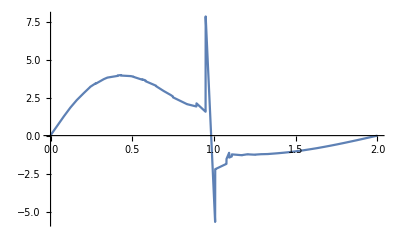

```mathematica
(*X Diffusion in middle of system, y=0.5, for nonuniform diffusion at t=0.4*)
tVV=0.4;
Plot[XderivNonUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

```mathematica
(*X Diffusion in middle of system, y=0.5, for uniform diffusion as comparison at t=0.4*)
```

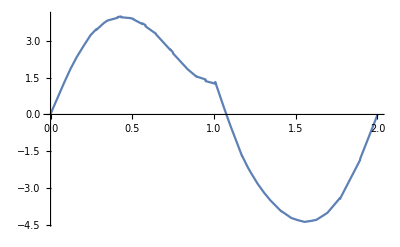

```mathematica
Plot[XderivUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

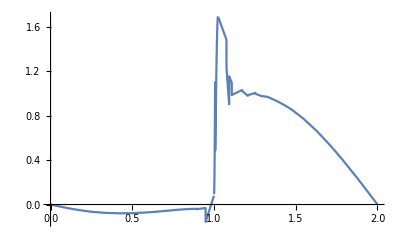

```mathematica
(*X Heat Flux in middle of system, y=0.5, for nonuniform diffusion at t=0.4*)
Plot[-XderivNonUniformDiffusion[tVV,x,0.5]*diffFunc[x],{x,0,2}]
```

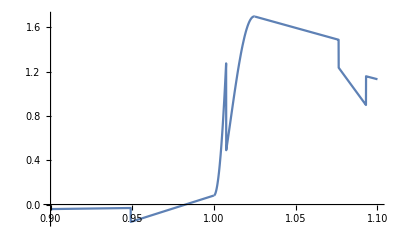

```mathematica
Plot[-XderivNonUniformDiffusion[tVV,x,0.5]*diffFunc[x],{x,0.9,1.1}]
```

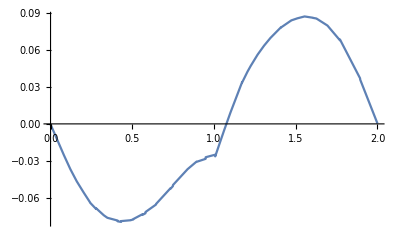

```mathematica
(*X Heat Flux in middle of system, y=0.5, for uniform diffusion as comparison at t=0.4*)
Plot[-XderivUniformDiffusion[tVV,x,0.5]*alphaSheet,{x,0,2}]
```

```mathematica
(*Diffusion at borders. should be near zero*)
Table[YderivNonUniformDiffusion[tVV,x,1],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0],{x,0,1,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5-epsilon],{x,1,2,.1}]
Table[YderivNonUniformDiffusion[tVV,x,0.5+epsilon],{x,1,2,.1}]
Table[XderivNonUniformDiffusion[tVV,0,y],{y,0,1,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5-epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,1,y],{y,0,0.5+epsilon,.1}]
Table[XderivNonUniformDiffusion[tVV,2,y],{y,0.5-epsilon,0.5+epsilon,.02}]
```

{0.000594678,-0.00605541,-0.0259744,0.00305999,-0.00736134,-0.0488535,-0.0856923,-0.00783662,-0.0118599,-0.0195261,-0.0523455}

{-0.0237529,0.0177627,0.019643,-0.0365654,-0.0462949,0.0919516,0.0570564,0.0346786,0.0225419,0.0082668,0.083956}

{11.0102,-0.0132752,0.0248847,-0.00338951,-0.000886556,-0.000665065,-0.00146838,-0.000569681,0.000361909,0.00037963,-0.000476508}

{-3.54952,-0.162695,-0.00497561,-0.00667005,-0.00302744,0.00252727,0.00158264,-0.0000206041,-0.000318398,-0.000377956,0.000475094}

{0.00135495,0.0180493,0.0222936,-0.00584851,-0.01255,0.0123392,-0.00221376,-0.00970522,0.0242181,0.0156878,-0.000885991}

{0.0336901,-0.0501802,-0.0622968,-0.0247143,2.81377}

{0.0336901,-0.0501802,-0.0622968,-0.0247143,2.81377,-4.07671,-1.66925}

{-0.000674798,-0.000223162,-0.000184289,-0.000145417,-0.000106544,-0.000399568,-0.000106683,-0.000145455,-0.000184226,-0.000222998,-0.000673441}

```mathematica
(*Diffusion at borders for uniform system as comparison. should be near zero*)
```

```mathematica
Table[YderivUniformDiffusion[tVV,x,1],{x,0,1,.1}]
Table[YderivUniformDiffusion[tVV,x,0],{x,0,1,.1}]
Table[YderivUniformDiffusion[tVV,x,0.5-epsilon],{x,1,2,.1}]
Table[YderivUniformDiffusion[tVV,x,0.5+epsilon],{x,1,2,.1}]
Table[XderivUniformDiffusion[tVV,0,y],{y,0,1,.1}]
Table[XderivUniformDiffusion[tVV,1,y],{y,0,0.5-epsilon,.1}]
Table[XderivUniformDiffusion[tVV,1,y],{y,0,0.5+epsilon,.1}]
Table[XderivUniformDiffusion[tVV,2,y],{y,0.5-epsilon,0.5+epsilon,.02}]
```

{0.000595777,-0.00606184,-0.0259995,0.00303565,-0.00741006,-0.0489803,-0.0858386,-0.00793522,-0.011895,-0.019442,-0.052425}

{-0.0237739,0.017774,0.0196697,-0.0365436,-0.0462719,0.0920569,0.0571352,0.0349532,0.0227017,0.00884163,0.0863359}

{6.55087,-0.322977,-0.000610534,0.00769263,0.00496449,-0.00791057,-0.0192778,-0.0120388,0.0096895,0.0148956,-0.0191628}

{-4.76695,-0.0596456,0.00459017,-0.00733917,-0.0135628,0.0158982,0.017472,-0.000144077,-0.00879037,-0.0148371,0.0191166}

{0.00134474,0.0180565,0.022301,-0.00584696,-0.0125371,0.0123583,-0.00219835,-0.00969542,0.0242254,0.0156986,-0.000887123}

{0.0350745,-0.0525054,-0.0772943,-0.0611856,1.04177}

{0.0350745,-0.0525054,-0.0772943,-0.0611856,1.04177,1.26518,3.2893}

{-0.0275491,-0.00929468,-0.00775524,-0.0062158,-0.00467637,-0.016547,-0.00466628,-0.00621135,-0.00775642,-0.00930149,-0.0275228}

```mathematica
(*Total Energy of system at a few time points to make sure that is conserved*)
```

```mathematica
Table[NIntegrate[valsNonUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{1.24627,1.35798,1.27124,1.20792,1.17095,1.14803,1.13246,1.12107,1.11232,1.10538}

```mathematica
Table[NIntegrate[valsUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{1.21344,1.21344,1.21344,1.21344,1.21344,1.21344,1.21344,1.21344,1.21344,1.21344}